## Exact Result

```mathematica
Y=-Pi w0^2/(e-e0)
```

-(π w0^2)/(e-e0)

```mathematica
K = Simplify[a Sqrt[e] Y/(1- G/Pi Y e)]
```

-(a √e π w0^2)/(e-e0+e G w0^2)

```mathematica
Kp=FullSimplify[D[K,e]]
```

(a π w0^2 (e+e0+e G w0^2))/(2 √e (e-e0+e G w0^2)^2)

```mathematica
Q1=Simplify[-Kp/(1+K^2),Assumptions->{e>0,G>0,w0>0,e0>0,a>0}]
```

-(a π w0^2 (e+e0+e G w0^2))/(2 √e (e0^2+a^2 e π^2 w0^4-2 e e0 (1+G w0^2)+(e+e G w0^2)^2))

```mathematica
Q1=Simplify[(a π w0^2 (e+e0+e G w0^2))/(2 √e (e0^2-2 e e0 (1+G w0^2)+(e+e G w0^2)^2))]
```

(a π w0^2 (e+e0+e G w0^2))/(2 √e (e-e0+e G w0^2)^2)

```mathematica
Expand[e0^2-2 e e0 (1+G w0^2)+(e+e G w0^2)^2]
```

e^2-2 e e0+e0^2+2 e^2 G w0^2-2 e e0 G w0^2+e^2 G^2 w0^4

```mathematica
Simplify[e^2-2 e e0+e0^2+2 e^2 G w0^2-2 e e0 G w0^2+e^2 G^2 w0^4]
```

(e-e0+e G w0^2)^2

```mathematica
Expand[((1+G w0^2)e-e0)^2]
```

e^2-2 e e0+e0^2+2 e^2 G w0^2-2 e e0 G w0^2+e^2 G^2 w0^4

```mathematica
Q1 Sqrt[e]/.{e->0}
```

-(a π w0^2)/(2 e0)

```mathematica
FullSimplify[Q1*Sqrt[e]/.{e0->0}, Assumptions->{w0>0}]
```

-(a π w0^2 (1+G w0^2))/(2 (a^2 π^2 w0^4+e (1+G w0^2)^2))

```mathematica
FullSimplify[Q1/.{w0->Sqrt[ w0^2-1/G]}, Assumptions->{G>0,w0>0,e0>0}]
```

-(a G π (-1+G w0^2) (e0+e G w0^2))/(2 √e (e0^2 G^2-2 e e0 G^3 w0^2+e (e G^4 w0^4+a^2 π^2 (-1+G w0^2)^2)))

```mathematica
Limit[(a π w0^2 (1+G w0^2))/(2 (a^2 π^2 w0^4+e (1+G w0^2)^2)),w0->Infinity]
```

(a G π)/(2 e G^2+2 a^2 π^2)

```mathematica
abar = N[(Pi/2^(3/2)/Gamma[5/4]/Gamma[1/2])^2]
```

0.477989

```mathematica
Clear[a]
```

```mathematica
G=Pi(abar^2-1/3)
```

-0.329428

```mathematica
Y2=-Pi (w1^2/(e-e1)+w2^2/(e-e2))
```

-π (w1^2/(e-e1)+w2^2/(e-e2))

```mathematica
Clear[G]
```

```mathematica
K2 = Simplify[a Sqrt[e] Y2/(1- G/Pi Y2 e)]
```

-(a √e π (w1^2/(e-e1)+w2^2/(e-e2)))/(1+e G (w1^2/(e-e1)+w2^2/(e-e2)))

```mathematica
Kp2=D[K2,e]
```

(a √e π (w1^2/(e-e1)+w2^2/(e-e2)) (e G (-w1^2/(e-e1)^2-w2^2/(e-e2)^2)+G (w1^2/(e-e1)+w2^2/(e-e2))))/((1+e G (w1^2/(e-e1)+w2^2/(e-e2)))^2)-(a √e π (-w1^2/(e-e1)^2-w2^2/(e-e2)^2))/(1+e G (w1^2/(e-e1)+w2^2/(e-e2)))-(a π (w1^2/(e-e1)+w2^2/(e-e2)))/(2 √e (1+e G (w1^2/(e-e1)+w2^2/(e-e2))))

```mathematica
Q=FullSimplify[-Kp2/(1+K2^2)]
```

-(a π ((e-e2)^2 w1^2 (e+e1+e G w1^2)+(e-e1) ((e-e1) (e+e2)+2 e (e-e2) G w1^2) w2^2+e (e-e1)^2 G w2^4))/(2 √e ((e-e2) (e-e1+e G w1^2)+e (e-e1) G w2^2)^2 (1+(a^2 e π^2 ((e-e2) w1^2+(e-e1) w2^2)^2)/(((e-e2) (e-e1+e G w1^2)+e (e-e1) G w2^2)^2)))

```mathematica
FullSimplify[Q/.{w1->Sqrt[w1^2-1/G],w2->Sqrt[w2^2-1/G]}]
```

-(a π ((e-e2)^2 (-1+G w1^2) (e1+e G w1^2)-(e-e1) ((e-e1) (e+e2)+2 e (e-e2) (-1+G w1^2)) (1-G w2^2)+e (e-e1)^2 (-1+G w2^2)^2))/(2 √e G (e1 e2-e G (e2 w1^2+e1 w2^2)+e^2 (-1+G (w1^2+w2^2)))^2 (1+(a^2 e π^2 (-2 e+e1+e2+e G w1^2-e2 G w1^2+(e-e1) G w2^2)^2)/(G^2 (e1 e2-e (e-e G (w1^2+w2^2)+G (e2 w1^2+e1 w2^2)))^2)))

```mathematica
FullSimplify[Q*Sqrt[e]/.{e1->0,e2->0}]
```

-(a π (w1^2+w2^2) (1+G (w1^2+w2^2)))/(2 (a^2 π^2 (w1^2+w2^2)^2+e (1+G (w1^2+w2^2))^2))

```mathematica
Simplify[Limit[-(a π (w1^2+w2^2) (1+G (w1^2+w2^2)))/(2 (a^2 π^2 (w1^2+w2^2)^2+e (1+G (w1^2+w2^2))^2))/.{w1->w2},w2->Infinity]]
```

-(a G π)/(2 e G^2+2 a^2 π^2)

```mathematica
Limit[Q,e->e1]
```

-(a π (2+G w1^2))/(2 √e1 (e1 G^2+a^2 π^2) w1^2)

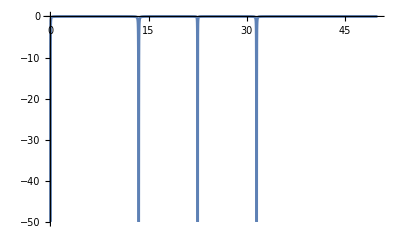

```mathematica
Plot[Q/.{w1->1,w2->1,w3->1,w4->1,G->-0.33,e1->10,e2->20,e3->35,e4->25,a->48},{e,0,50},PlotRange->{0,-50}]
```

```mathematica
|
```

```mathematica
FullSimplify[Sqrt[e] Q/.{e->0}]
```

-1/2 a π (w1^2/e1+w2^2/e2+w3^2/e3)

## Plotting

```mathematica
W0=PDF[NormalDistribution[0,2],x]
```

(ⅇ^(-x^2/8))/(2 √(2 π))

```mathematica
test=W0 (W0/.{x->y/x})
```

(ⅇ^(-x^2/8-y^2/(8 x^2)))/(8 π)

```mathematica
E0=PDF[UniformDistribution[{-2,2}],z y]
```

Piecewise[{{1/4, -2≤y z≤2}, {0, True}}]

```mathematica
product[z_]:=NIntegrate[W0 (W0/.{x->z/x})/Abs[x],{x,-Infinity,Infinity}]
```

```mathematica
product[1]
```

0.122669

```mathematica
squareW=PDF[GammaDistribution[1/2,2s^2],x]
```

Piecewise[{{(ⅇ^(-x/(2 s^2)))/(√(2 π) √(s^2) √x), x>0}, {0, True}}]

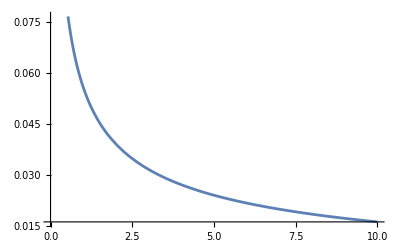

```mathematica
Plot[ⅇ^(-x/s)/(√π √s √x)/.{s->100},{x,0,10}]
```

```mathematica
Limit[ⅇ^(-x/s)/(√π √s √x)/.{s->100},x->0]
```

Indeterminate

```mathematica
Integrate[(ⅇ^(-y/(2 s^2)))/(√(2 π) s √y)/.{s->100},{y,0,Infinity}]
```

1

```mathematica
ratio:=NIntegrate[1/4y ⅇ^(-y/2)/(√(2 π) √y),{y,0,2/z}]
```

```mathematica
PDF[ratio,x]
```

NIntegrate::nlim: y = 2./z is not a valid limit of integration.

PDF[NIntegrate[(y ⅇ^(-y/2))/(4 (√(2 π) √y)),{y,0,2/z}],x]

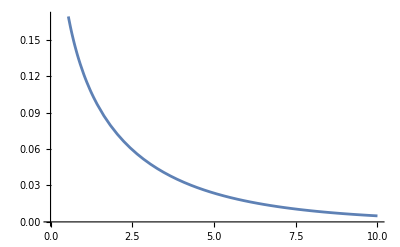

```mathematica
Plot[product[x],{x,0,10}]
```

```mathematica
Plot[squareW,{y,0,10}]
```

-Graphics-

```mathematica
ratio/.{z->3}
```

NIntegrate::nlim: y = 2./z is not a valid limit of integration.

0.0297463

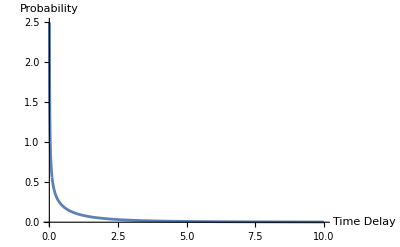

```mathematica
p1=Plot[NIntegrate[1/4y ⅇ^(-z y/2)/(√(2 π) √(z y)),{y,0,2}],{z,0,0.1},PlotPoints->1000,PlotRange->{{0,10},{0,2.5}}];p2=Plot[NIntegrate[1/4y ⅇ^(-z y/2)/(√(2 π) √(z y)),{y,0,2}],{z,0.1,10},PlotRange->{{0,10},{0,2.5}}];
Show[p1,p2,PlotRange->All,AxesLabel->{"Time Delay","Probability"}]
```

```mathematica
σ=0.001
```

0.001

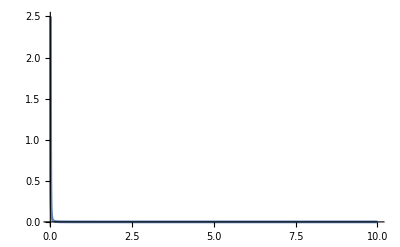

```mathematica
p3=Plot[NIntegrate[1/4y ⅇ^(-z y/σ)/(√(σ π) √(z y)),{y,0,2}],{z,0,0.1},PlotPoints->1000,PlotRange->{{0,10},{0,2.5}}];p4=Plot[NIntegrate[1/4y ⅇ^(-z y/σ)/(√(σ π) √(z y)),{y,0,2}],{z,0.1,10},PlotRange->{{0,10},{0,2.5}}];
Show[p3,p4,PlotRange->All]
```

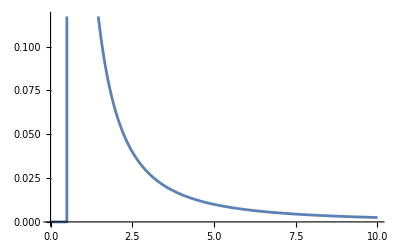

```mathematica
Plot[Integrate[1/4y DiracDelta[z y-1],{y,0,2}],{z,0,10}]
```

```mathematica
NIntegrate[1/4y (ⅇ^(-z y/2)/(√(2 π) √(z y))).,{z->0},{y,0,2}]
```

```mathematica
Integrate[y E^(-c y^2),{y,0,Infinity}]
```

ConditionalExpression[1/(2 c), Re[c]>0]

```mathematica
Integrate[Sqrt[y] E^(-c (y-d)^2),{y,0,Infinity},Assumptions->{c>0,d>0}]
```

(ⅇ^(-c d^2) (Gamma[3/4] Hypergeometric1F1[3/4,1/2,c d^2]+2 √c d Gamma[5/4] Hypergeometric1F1[5/4,3/2,c d^2]))/(2 c^(3/4))

```mathematica
TeXForm[(ⅇ^(-c d^2) (Gamma[3/4] Hypergeometric1F1[3/4,1/2,c d^2]+2 √c d Gamma[5/4] Hypergeometric1F1[5/4,3/2,c d^2]))/(2 c^(3/4))]
```

\frac{e^{-c d^2} \left(\Gamma \left(\frac{3}{4}\right) \, _1F_1\left(\frac{3}{4};\frac{1}{2};c d^2\right)+2 \sqrt{c} d \Gamma
   \left(\frac{5}{4}\right) \, _1F_1\left(\frac{5}{4};\frac{3}{2};c d^2\right)\right)}{2 c^{3/4}}

```mathematica
m=1
alpha=1
x=1
```

1

1

1

```mathematica
eq = (ⅇ^(-c d^2) (Gamma[3/4] Hypergeometric1F1[3/4,1/2,c d^2]+2 √c d Gamma[5/4] Hypergeometric1F1[5/4,3/2,c d^2]))/(2 c^(3/4))*E^(-alpha^2 z^2/(8 x^4 m^2))/Sqrt[z]/(2Pi alpha x m^2)/.{c->1/(2 alpha^2 x^4 m^2),d->alpha^2 z/(2x^2)}
```

(ⅇ^(-z^2/4) (Gamma[3/4] Hypergeometric1F1[3/4,1/2,z^2/8]+(z Gamma[5/4] Hypergeometric1F1[5/4,3/2,z^2/8])/(√2)))/(2 2^(1/4) π √z)

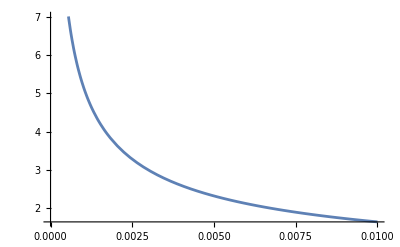

```mathematica
Plot[eq,{z,0,0.01}]
```

```mathematica
N[Sqrt[2]/Pi*2]
```

0.900316

```mathematica
NIntegrate[eq,{z,0,1000}]
```

0.776887

```mathematica
NIntegrate[eq,{z,0,0.38}]/NIntegrate[eq,{z,0,14}]
```

0.507695

```mathematica
Integrate[Sqrt[y]E^(-(y^2-z y)/(2)),{y,0,Infinity},Assumptions->{z>0}]
```

(√2 Gamma[3/4] Hypergeometric1F1[3/4,1/2,z^2/8]+z Gamma[5/4] Hypergeometric1F1[5/4,3/2,z^2/8])/2^(3/4)

```mathematica
eq2=(√2 Gamma[3/4] Hypergeometric1F1[3/4,1/2,z^2/8]+z Gamma[5/4] Hypergeometric1F1[5/4,3/2,z^2/8])/2^(3/4)/Sqrt[z]/(2Pi alpha x m^2)
```

(√2 Gamma[3/4] Hypergeometric1F1[3/4,1/2,z^2/8]+z Gamma[5/4] Hypergeometric1F1[5/4,3/2,z^2/8])/(2 2^(3/4) π √z)

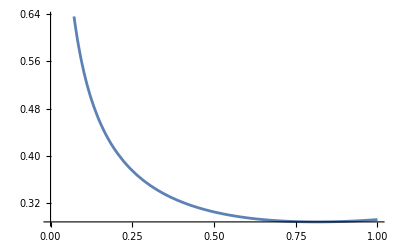

```mathematica
Plot[eq2,{z,0,1}]
```